```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
optionC=If[StringFreeQ[$System,"Windows"],"-c","/c"];
sizes = {4,10,15,20,22,25,27,30(*,32,35,37,40*)};
fptass = Function[x,"FPTAS"<>ToString[x]]/@{1,2,3};
solvers =Flatten[{"bb","valueDecomposition", "greedy", "redux", fptass, "FPTAS32"}];
prefixes = {"NK", "ZKC"};
threads = 3;
```

```mathematica
solve[prefix_, size_, solver_]:=(
args = "--source ./"<>prefix<>"/"<>prefix<>ToString[size]<>"_inst.dat --solver " <> solver<>" --threads "<>ToString[threads];


error = ToString[RunProcess[ {$SystemShell, optionC,"./cmake-build-debug/hw2 " <> args}, "StandardError"]];
If[error!="",args <> " Error: " <> error, args <> " Completed"]
);
(*--------------------------------geather---------------------------*)
geather[dir_,prefix_, suffix_,size_,solver_, index_, type_]:=(
out = dir<>If[dir=="","","/"]<>solver<>If[solver=="","","/"]<>prefix<>"/"<>prefix<>ToString[size]<>"_"<>suffix<>".dat";
stream = OpenRead[out];

results = {};
lastId = 0;

Do[(
tmp = ReadLine[stream];
If[tmp == EndOfFile, Break[]];

id=Read[StringToStream[ StringSplit[tmp][[1]] ],Number];
If[id == lastId+1,(
lastId=id;
AppendTo[results,Read[StringToStream[ StringSplit[tmp][[index]] ],type]];
)]
),
Infinity];

Close[stream];

results
);
geatherTime[prefix_,size_, solver_]:=(
geather["OUT",prefix,"inst",size,solver,-1, Real]
);
geatherCount[prefix_,size_, solver_]:=(
geather["OUT",prefix,"inst",size,solver,-2, Number]
);
geatherRelativeError[prefix_,size_, solver_]:=(
myres=geather["OUT",prefix,"inst",size, solver, 4, Number];
res=geather["",prefix,"sol",size,"",3,Number];

error={};
For[index=1, index<=Length[myres],index++,
AppendTo[error,
If[res[[index]]==0,
0,
1-myres[[index]] / res[[index]]
]
];
];
error
);
myExport[what_,name_]:=(
Export["OUT/"<>name<>".pdf",what];
);
(*--------------------------------ListPlot---------------------------*)
timeListPlot[dataset_,prefix_, selectedSolvers_, style_]:=(

selects = Flatten[Function[x,{
Select[fullSet, #prefix==prefix && #solver ==x &][ All, {#size,#timeMean}&],
Select[fullSet, #prefix==prefix && #solver ==x &][ All, {#size,#timeMax}&]
}]/@selectedSolvers];

legends = Flatten[Function[x,{
x <> " - Mean", x <> " - Max"
}]/@selectedSolvers];

plotStyle = Flatten[Function[x,{
{x},{x,Dotted}
}]/@style,1];

ListPlot[selects,Joined->True,PlotLegends->legends,PlotStyle->plotStyle,  PlotRange->All,PlotLabel->"time to solve a problem ("<>prefix<>")",AxesLabel->{None,"s"}]
);
countListPlot[dataset_,prefix_, selectedSolvers_, style_]:=(

selects = Flatten[Function[x,{
Select[fullSet, #prefix==prefix && #solver ==x &][ All, {#size,#countMean}&],
Select[fullSet, #prefix==prefix && #solver ==x &][ All, {#size,#countMax}&]
}]/@selectedSolvers];

legends = Flatten[Function[x,{
x <> " - Mean", x <> " - Max"
}]/@selectedSolvers];

plotStyle = Flatten[Function[x,{
{x},{x,Dotted}
}]/@style,1];

ListPlot[
selects,Joined->True,PlotLegends->legends, PlotStyle->plotStyle,PlotRange->All,PlotLabel->"number of operations ("<>prefix<>")"]
);
errorMeanListPlot[dataset_,prefix_, selectedSolvers_, style_]:=(

selects = Function[x,
Select[fullSet, #prefix==prefix && #solver ==x &][ All, {#size,#errorMean}&]
]/@selectedSolvers;

legends = Function[x,
x <> " - Mean"
]/@selectedSolvers;

plotStyle = style;

ListPlot[
selects,Joined->True,PlotLegends->legends, PlotStyle->plotStyle,PlotRange->All,PlotLabel->"error ("<>prefix<>")"]
);
errorListPlot[dataset_,prefix_, selectedSolvers_, style_]:=(

selects = Flatten[Function[x,{
Select[fullSet, #prefix==prefix && #solver ==x &][ All, {#size,#errorMean}&],
Select[fullSet, #prefix==prefix && #solver ==x &][ All, {#size,#errorMax}&]
}]/@selectedSolvers];

legends = Flatten[Function[x,{
x <> " - Mean", x <> " - Max"
}]/@selectedSolvers];

plotStyle = Flatten[Function[x,{
{x},{x,Dotted}
}]/@style,1];

ListPlot[
selects,Joined->True,PlotLegends->legends, PlotStyle->plotStyle,PlotRange->All,PlotLabel->"error ("<>prefix<>")"]
);
(*--------------------------------Histogram---------------------------*)
timeHistogram[dataset_,prefix_,size_,selectedSolvers_, steps_, style_]:=(

selects = Flatten[Function[x,{
Normal[Select[dataset, #prefix==prefix&& #solver ==x && #size == size &][ All, #time&][Flatten]]
}]/@selectedSolvers,1];

Histogram[selects,steps, ChartLegends->selectedSolvers, ChartStyle->style, PlotRange->All, PlotLabel->"time to solve a problem ("<>prefix<>ToString[size]<>")",AxesLabel->{"s",None}]
);
countHistogram[dataset_,prefix_,size_,selectedSolvers_,steps_,style_]:=(

selects = Flatten[Function[x,{
Normal[Select[dataset, #prefix==prefix&& #solver ==x && #size == size &][ All, #count&][Flatten]]
}]/@selectedSolvers,1];


Histogram[selects,steps, ChartLegends->selectedSolvers, ChartStyle->style, PlotRange->All, PlotLabel->"number of operations ("<>prefix<>ToString[size]<>")"]
);
errorHistogram[dataset_,prefix_,size_,selectedSolvers_,steps_,style_]:=(

selects = Flatten[Function[x,{
Normal[Select[dataset, #prefix==prefix&& #solver ==x && #size == size &][ All, #error&][Flatten]]
}]/@selectedSolvers,1];


Histogram[selects,steps, ChartLegends->selectedSolvers, ChartStyle->style, PlotRange->All, PlotLabel->"errors ("<>prefix<>ToString[size]<>")"]
);
```

```mathematica
(*-----------------SOLVE-----------------*)
Do[Print[ solve[k,i, j]  ],{i,sizes},{k, prefixes}, {j,solvers} ];
Print["---evaluation completed---"];
(*-----------------SOLVE-----------------*)
```

```mathematica
(*-----------------GEATHER-DATA-----------------*)
fullSet = Dataset[{}];

Do[AppendTo[fullSet, <|"prefix"->k,"solver"->j,"size"->i,"count"->geatherCount[k,i,j],"time"->geatherTime[k, i, j ], "error"->geatherRelativeError[k, i, j ]|>], {i,sizes}, {j,solvers}, {k, prefixes} ];

fullSet = fullSet[All,<|#, "countMean"->Mean[#count], "countMax"->Max[#count], "timeMean"->Mean[#time], "timeMax"->Max[#time], "errorMean"->Mean[#error], "errorMax"->Max[#error]|>&];
(*-----------------GEATHER-DATA-----------------*)
```

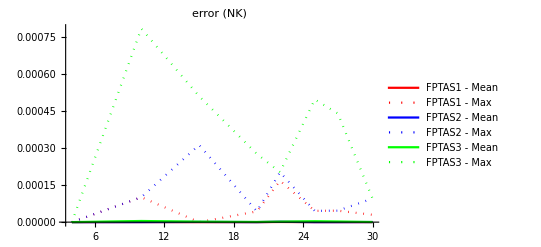

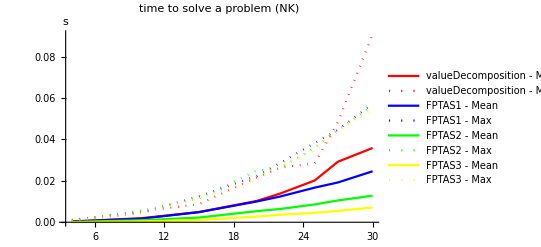

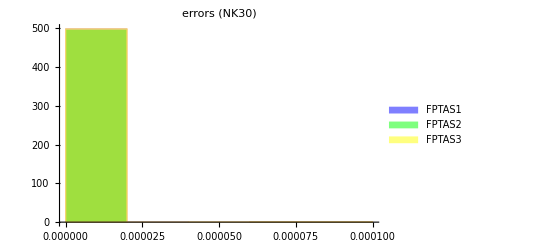

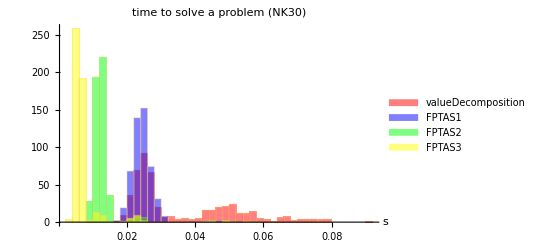

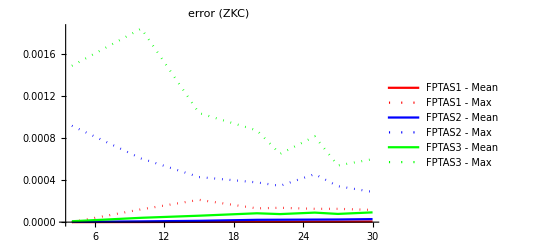

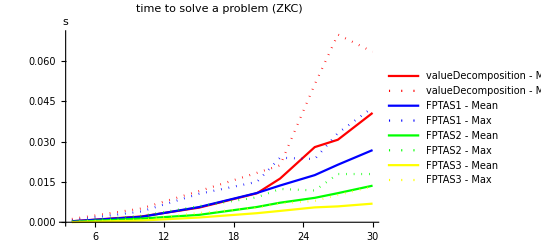

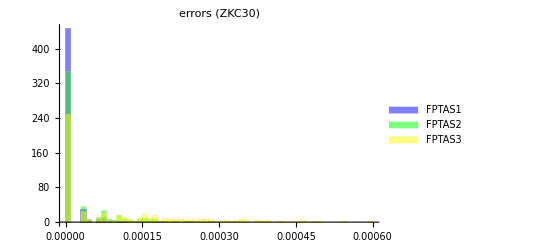

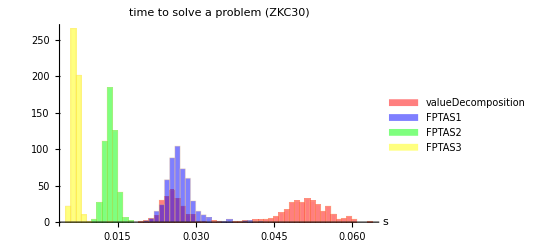

```mathematica
nkfptaserrl = errorListPlot[fullSet,"NK", fptass, {Red, Blue, Green}]
nkfptastimel = timeListPlot[fullSet,"NK", Flatten[{"valueDecomposition",fptass}], {Red, Blue, Green, Yellow}]

nkfpterrh = errorHistogram[fullSet,"NK", Last[sizes],fptass, 50, {Blue, Green, Yellow}]
nkfpttimeh = timeHistogram[fullSet,"NK", Last[sizes],Flatten[{"valueDecomposition",fptass}], 50, {Red, Blue, Green, Yellow}]

zkcfptaserrl = errorListPlot[fullSet,"ZKC", fptass, {Red, Blue, Green}]
zkcfptastimel = timeListPlot[fullSet,"ZKC", Flatten[{"valueDecomposition",fptass}], {Red, Blue, Green, Yellow}]

zkcfpterrh = errorHistogram[fullSet,"ZKC", Last[sizes],fptass, 50, {Blue, Green, Yellow}]
zkcfpttimeh = timeHistogram[fullSet,"ZKC", Last[sizes],Flatten[{"valueDecomposition",fptass}], 50, {Red, Blue, Green, Yellow}]
```

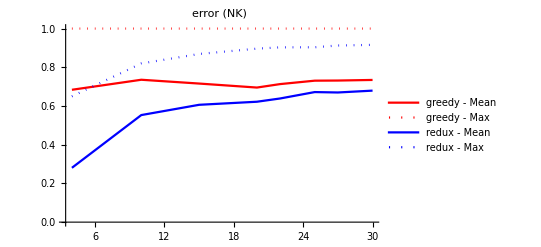

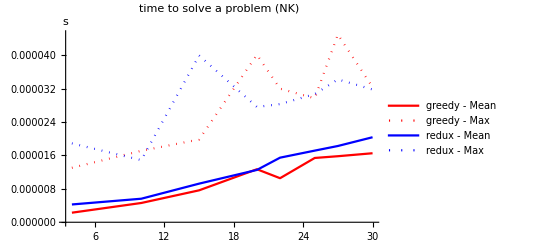

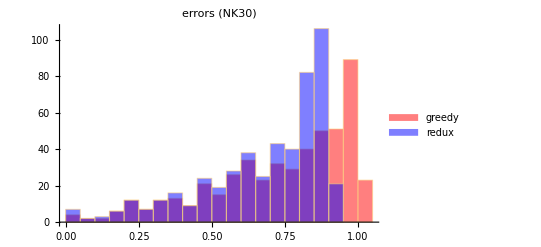

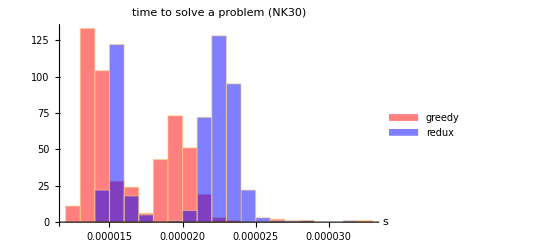

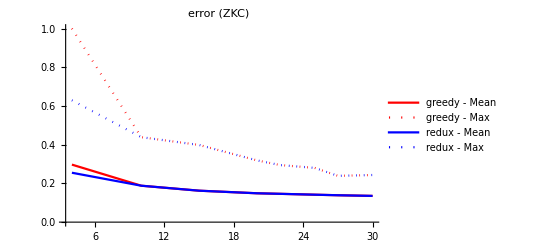

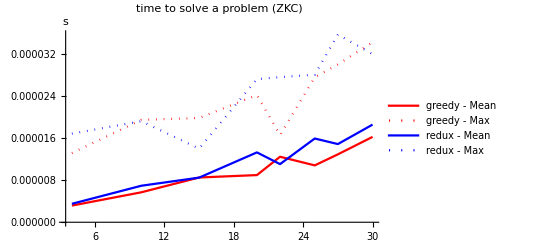

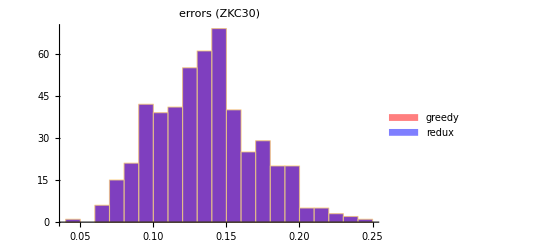

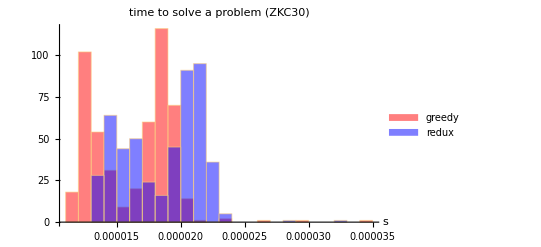

```mathematica
nkgrerrl = errorListPlot[fullSet,"NK", {"greedy", "redux"}, {Red, Blue}]
nkgrtimel = timeListPlot[fullSet,"NK", {"greedy", "redux"}, {Red, Blue}]

nkgrerrh=errorHistogram[fullSet,"NK", Last[sizes],{"greedy", "redux"}, 22, {Red, Blue}]
nkgrtimeh=timeHistogram[fullSet,"NK", Last[sizes],{"greedy", "redux"}, 22, {Red, Blue}]

zkcgrerrl = errorListPlot[fullSet,"ZKC", {"greedy", "redux"}, {Red, Blue}]
zkcgrtimel = timeListPlot[fullSet,"ZKC", {"greedy", "redux"}, {Red, Blue}]

zkcgrerrh = errorHistogram[fullSet,"ZKC", Last[sizes],{"greedy", "redux"}, 22, {Red, Blue}]
zkcgrtimeh = timeHistogram[fullSet,"ZKC", Last[sizes],{"greedy", "redux"}, 22, {Red, Blue}]
```

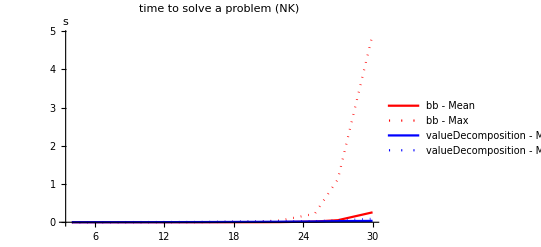

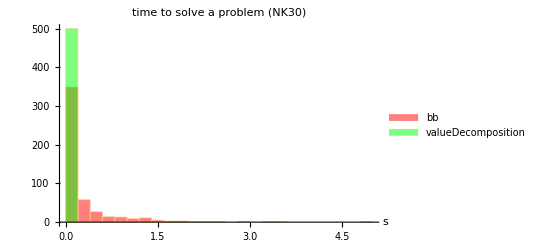

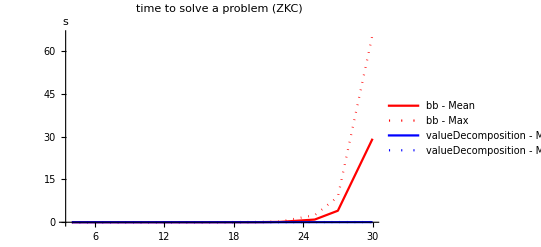

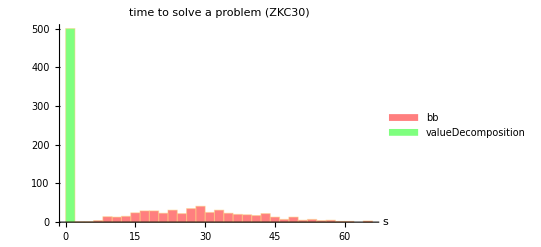

```mathematica
nkbvtimel = timeListPlot[fullSet,"NK", {"bb","valueDecomposition"}, {Red, Blue}]
nkbvtimeh = timeHistogram[fullSet,"NK", Last[sizes],{"bb","valueDecomposition"}, 22, {Red, Green}]

zkcbvtimel = timeListPlot[fullSet,"ZKC", {"bb","valueDecomposition"}, {Red, Blue}]
zkcbvtimeh = timeHistogram[fullSet,"ZKC", Last[sizes],{"bb","valueDecomposition"}, 22, {Red, Green}]
```

```mathematica
myExport[nkfptaserrl,"nkfptaserrl"]
myExport[nkfptastimel,"nkfptastimel"]
myExport[nkfpterrh,"nkfpterrh"]
myExport[nkfpttimeh,"nkfpttimeh"]
myExport[nkgrerrl,"nkgrerrl"]
myExport[nkgrtimel,"nkgrtimel"]
myExport[nkgrerrh,"nkgrerrh"]
myExport[nkgrtimeh,"nkgrtimeh"]
myExport[nkbvtimel,"nkbvtimel"]
myExport[nkbvtimeh,"nkbvtimeh"]
```

```mathematica
myExport[zkcfptaserrl,"zkcfptaserrl"]
myExport[zkcfptastimel,"zkcfptastimel"]
myExport[zkcfpterrh,"zkcfpterrh"]
myExport[zkcfpttimeh,"zkcfpttimeh"]
myExport[zkcgrerrl,"zkcgrerrl"]
myExport[zkcgrtimel,"zkcgrtimel"]
myExport[zkcgrerrh,"zkcgrerrh"]
myExport[zkcgrtimeh,"zkcgrtimeh"]
myExport[zkcbvtimel,"zkcbvtimel"]
myExport[zkcbvtimeh,"zkcbvtimeh"]
```

```mathematica
myExport[ListPlot[{1,2,3,4,5,6}],"test"]
```